### Vector definitions

```mathematica
S1 = {S1x[t],S1y[t],S1z[t]};
S2 = {S2x[t],S2y[t],S2z[t]};
J={Jx,Jy,Jz};
```

```mathematica
L=J-S1-S2;
```

```mathematica
S0=(1+1/q)S1+(1+q)S2;
```

```mathematica
λ=Simplify[Dot[L,S0]/Norm[L]^2]
```

((1+q) ((Jx-S1x[t]-S2x[t]) (S1x[t]+q S2x[t])+(Jy-S1y[t]-S2y[t]) (S1y[t]+q S2y[t])+(Jz-S1z[t]-S2z[t]) (S1z[t]+q S2z[t])))/(q (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2))

### Differential equations

```mathematica
dS1=Simplify[Cross[1/(2 d^3)((4+3/q-3/(q+1)λ)L+S2),S1]];
dS2=Simplify[Cross[1/(2 d^3)((4+3q-(3q)/(q+2)λ)L+S1),S2]];
```

### Numerical solution

```mathematica
solution=With[{Jx=1,Jy=1,Jz=2,d=0.8,q=0.4},NDSolve[{
S1x'[t]==(-3 Jz Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t]-4 Jz q Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t]+3 Jx Jz S1x[t] S1y[t]-3 Jz S1x[t]^2 S1y[t]+3 Jy Jz S1y[t]^2-3 Jz S1y[t]^3+3 Jy Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t]+4 Jy q Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t]-3 Jx Jy S1x[t] S1z[t]+3 Jy S1x[t]^2 S1z[t]-3 Jy^2 S1y[t] S1z[t]+3 Jz^2 S1y[t] S1z[t]+3 Jy S1y[t]^2 S1z[t]-3 Jy Jz S1z[t]^2-3 Jz S1y[t] S1z[t]^2+3 Jy S1z[t]^3+3 Jx Jz q S1y[t] S2x[t]-3 Jz S1x[t] S1y[t] S2x[t]-3 Jz q S1x[t] S1y[t] S2x[t]-3 Jx Jy q S1z[t] S2x[t]+3 Jy S1x[t] S1z[t] S2x[t]+3 Jy q S1x[t] S1z[t] S2x[t]-3 Jz q S1y[t] S2x[t]^2+3 Jy q S1z[t] S2x[t]^2+3 Jy Jz q S1y[t] S2y[t]-3 Jz S1y[t]^2 S2y[t]-3 Jz q S1y[t]^2 S2y[t]-3 Jy^2 q S1z[t] S2y[t]-3 Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2y[t]-3 q Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2y[t]+3 Jx S1x[t] S1z[t] S2y[t]-3 S1x[t]^2 S1z[t] S2y[t]+6 Jy S1y[t] S1z[t] S2y[t]+3 Jy q S1y[t] S1z[t] S2y[t]-3 S1y[t]^2 S1z[t] S2y[t]+3 Jz S1z[t]^2 S2y[t]-3 S1z[t]^3 S2y[t]+3 Jx q S1z[t] S2x[t] S2y[t]-3 S1x[t] S1z[t] S2x[t] S2y[t]-3 q S1x[t] S1z[t] S2x[t] S2y[t]-3 q S1z[t] S2x[t]^2 S2y[t]-3 Jz q S1y[t] S2y[t]^2+6 Jy q S1z[t] S2y[t]^2-3 S1y[t] S1z[t] S2y[t]^2-3 q S1y[t] S1z[t] S2y[t]^2-3 q S1z[t] S2y[t]^3+3 Jz^2 q S1y[t] S2z[t]+3 Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2z[t]+3 q Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2z[t]-3 Jx S1x[t] S1y[t] S2z[t]+3 S1x[t]^2 S1y[t] S2z[t]-3 Jy S1y[t]^2 S2z[t]+3 S1y[t]^3 S2z[t]-3 Jy Jz q S1z[t] S2z[t]-6 Jz S1y[t] S1z[t] S2z[t]-3 Jz q S1y[t] S1z[t] S2z[t]+3 Jy S1z[t]^2 S2z[t]+3 Jy q S1z[t]^2 S2z[t]+3 S1y[t] S1z[t]^2 S2z[t]-3 Jx q S1y[t] S2x[t] S2z[t]+3 S1x[t] S1y[t] S2x[t] S2z[t]+3 q S1x[t] S1y[t] S2x[t] S2z[t]+3 q S1y[t] S2x[t]^2 S2z[t]-3 Jy q S1y[t] S2y[t] S2z[t]+3 S1y[t]^2 S2y[t] S2z[t]+3 q S1y[t]^2 S2y[t] S2z[t]+3 Jz q S1z[t] S2y[t] S2z[t]-3 S1z[t]^2 S2y[t] S2z[t]-3 q S1z[t]^2 S2y[t] S2z[t]+3 q S1y[t] S2y[t]^2 S2z[t]-6 Jz q S1y[t] S2z[t]^2+3 Jy q S1z[t] S2z[t]^2+3 S1y[t] S1z[t] S2z[t]^2+3 q S1y[t] S1z[t] S2z[t]^2-3 q S1z[t] S2y[t] S2z[t]^2+3 q S1y[t] S2z[t]^3+Abs[Jx-S1x[t]-S2x[t]]^2 (S1z[t] (Jy (3+4 q)-3 (1+q) S2y[t])+S1y[t] (-Jz (3+4 q)+3 (1+q) S2z[t]))+Abs[Jy-S1y[t]-S2y[t]]^2 (S1z[t] (Jy (3+4 q)-3 (1+q) S2y[t])+S1y[t] (-Jz (3+4 q)+3 (1+q) S2z[t])))/(2 d^3 q (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2)),S1y'[t]==(3 Jz Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t]+4 Jz q Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t]-3 Jx Jz S1x[t]^2+3 Jz S1x[t]^3-3 Jy Jz S1x[t] S1y[t]+3 Jz S1x[t] S1y[t]^2-3 Jx Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t]-4 Jx q Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t]+3 Jx^2 S1x[t] S1z[t]-3 Jz^2 S1x[t] S1z[t]-3 Jx S1x[t]^2 S1z[t]+3 Jx Jy S1y[t] S1z[t]-3 Jx S1y[t]^2 S1z[t]+3 Jx Jz S1z[t]^2+3 Jz S1x[t] S1z[t]^2-3 Jx S1z[t]^3-3 Jx Jz q S1x[t] S2x[t]+3 Jz S1x[t]^2 S2x[t]+3 Jz q S1x[t]^2 S2x[t]+3 Jx^2 q S1z[t] S2x[t]+3 Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2x[t]+3 q Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2x[t]-6 Jx S1x[t] S1z[t] S2x[t]-3 Jx q S1x[t] S1z[t] S2x[t]+3 S1x[t]^2 S1z[t] S2x[t]-3 Jy S1y[t] S1z[t] S2x[t]+3 S1y[t]^2 S1z[t] S2x[t]-3 Jz S1z[t]^2 S2x[t]+3 S1z[t]^3 S2x[t]+3 Jz q S1x[t] S2x[t]^2-6 Jx q S1z[t] S2x[t]^2+3 S1x[t] S1z[t] S2x[t]^2+3 q S1x[t] S1z[t] S2x[t]^2+3 q S1z[t] S2x[t]^3-3 Jy Jz q S1x[t] S2y[t]+3 Jz S1x[t] S1y[t] S2y[t]+3 Jz q S1x[t] S1y[t] S2y[t]+3 Jx Jy q S1z[t] S2y[t]-3 Jx S1y[t] S1z[t] S2y[t]-3 Jx q S1y[t] S1z[t] S2y[t]-3 Jy q S1z[t] S2x[t] S2y[t]+3 S1y[t] S1z[t] S2x[t] S2y[t]+3 q S1y[t] S1z[t] S2x[t] S2y[t]+3 Jz q S1x[t] S2y[t]^2-3 Jx q S1z[t] S2y[t]^2+3 q S1z[t] S2x[t] S2y[t]^2-3 Jz^2 q S1x[t] S2z[t]-3 Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2z[t]-3 q Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2z[t]+3 Jx S1x[t]^2 S2z[t]-3 S1x[t]^3 S2z[t]+3 Jy S1x[t] S1y[t] S2z[t]-3 S1x[t] S1y[t]^2 S2z[t]+3 Jx Jz q S1z[t] S2z[t]+6 Jz S1x[t] S1z[t] S2z[t]+3 Jz q S1x[t] S1z[t] S2z[t]-3 Jx S1z[t]^2 S2z[t]-3 Jx q S1z[t]^2 S2z[t]-3 S1x[t] S1z[t]^2 S2z[t]+3 Jx q S1x[t] S2x[t] S2z[t]-3 S1x[t]^2 S2x[t] S2z[t]-3 q S1x[t]^2 S2x[t] S2z[t]-3 Jz q S1z[t] S2x[t] S2z[t]+3 S1z[t]^2 S2x[t] S2z[t]+3 q S1z[t]^2 S2x[t] S2z[t]-3 q S1x[t] S2x[t]^2 S2z[t]+3 Jy q S1x[t] S2y[t] S2z[t]-3 S1x[t] S1y[t] S2y[t] S2z[t]-3 q S1x[t] S1y[t] S2y[t] S2z[t]-3 q S1x[t] S2y[t]^2 S2z[t]+6 Jz q S1x[t] S2z[t]^2-3 Jx q S1z[t] S2z[t]^2-3 S1x[t] S1z[t] S2z[t]^2-3 q S1x[t] S1z[t] S2z[t]^2+3 q S1z[t] S2x[t] S2z[t]^2-3 q S1x[t] S2z[t]^3+Abs[Jx-S1x[t]-S2x[t]]^2 (S1z[t] (-Jx (3+4 q)+3 (1+q) S2x[t])+S1x[t] (Jz (3+4 q)-3 (1+q) S2z[t]))+Abs[Jy-S1y[t]-S2y[t]]^2 (S1z[t] (-Jx (3+4 q)+3 (1+q) S2x[t])+S1x[t] (Jz (3+4 q)-3 (1+q) S2z[t])))/(2 d^3 q (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2)),S1z'[t]==(-3 Jy Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t]-4 Jy q Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t]+3 Jx Jy S1x[t]^2-3 Jy S1x[t]^3+3 Jx Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t]+4 Jx q Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t]-3 Jx^2 S1x[t] S1y[t]+3 Jy^2 S1x[t] S1y[t]+3 Jx S1x[t]^2 S1y[t]-3 Jx Jy S1y[t]^2-3 Jy S1x[t] S1y[t]^2+3 Jx S1y[t]^3+3 Jy Jz S1x[t] S1z[t]-3 Jx Jz S1y[t] S1z[t]-3 Jy S1x[t] S1z[t]^2+3 Jx S1y[t] S1z[t]^2+3 Jx Jy q S1x[t] S2x[t]-3 Jy S1x[t]^2 S2x[t]-3 Jy q S1x[t]^2 S2x[t]-3 Jx^2 q S1y[t] S2x[t]-3 Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2x[t]-3 q Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2x[t]+6 Jx S1x[t] S1y[t] S2x[t]+3 Jx q S1x[t] S1y[t] S2x[t]-3 S1x[t]^2 S1y[t] S2x[t]+3 Jy S1y[t]^2 S2x[t]-3 S1y[t]^3 S2x[t]+3 Jz S1y[t] S1z[t] S2x[t]-3 S1y[t] S1z[t]^2 S2x[t]-3 Jy q S1x[t] S2x[t]^2+6 Jx q S1y[t] S2x[t]^2-3 S1x[t] S1y[t] S2x[t]^2-3 q S1x[t] S1y[t] S2x[t]^2-3 q S1y[t] S2x[t]^3+3 Jy^2 q S1x[t] S2y[t]+3 Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2y[t]+3 q Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2y[t]-3 Jx S1x[t]^2 S2y[t]+3 S1x[t]^3 S2y[t]-3 Jx Jy q S1y[t] S2y[t]-6 Jy S1x[t] S1y[t] S2y[t]-3 Jy q S1x[t] S1y[t] S2y[t]+3 Jx S1y[t]^2 S2y[t]+3 Jx q S1y[t]^2 S2y[t]+3 S1x[t] S1y[t]^2 S2y[t]-3 Jz S1x[t] S1z[t] S2y[t]+3 S1x[t] S1z[t]^2 S2y[t]-3 Jx q S1x[t] S2x[t] S2y[t]+3 S1x[t]^2 S2x[t] S2y[t]+3 q S1x[t]^2 S2x[t] S2y[t]+3 Jy q S1y[t] S2x[t] S2y[t]-3 S1y[t]^2 S2x[t] S2y[t]-3 q S1y[t]^2 S2x[t] S2y[t]+3 q S1x[t] S2x[t]^2 S2y[t]-6 Jy q S1x[t] S2y[t]^2+3 Jx q S1y[t] S2y[t]^2+3 S1x[t] S1y[t] S2y[t]^2+3 q S1x[t] S1y[t] S2y[t]^2-3 q S1y[t] S2x[t] S2y[t]^2+3 q S1x[t] S2y[t]^3+Abs[Jx-S1x[t]-S2x[t]]^2 (S1y[t] (Jx (3+4 q)-3 (1+q) S2x[t])+S1x[t] (-Jy (3+4 q)+3 (1+q) S2y[t]))+Abs[Jy-S1y[t]-S2y[t]]^2 (S1y[t] (Jx (3+4 q)-3 (1+q) S2x[t])+S1x[t] (-Jy (3+4 q)+3 (1+q) S2y[t]))+3 Jy Jz q S1x[t] S2z[t]-3 Jx Jz q S1y[t] S2z[t]-3 Jy S1x[t] S1z[t] S2z[t]-3 Jy q S1x[t] S1z[t] S2z[t]+3 Jx S1y[t] S1z[t] S2z[t]+3 Jx q S1y[t] S1z[t] S2z[t]+3 Jz q S1y[t] S2x[t] S2z[t]-3 S1y[t] S1z[t] S2x[t] S2z[t]-3 q S1y[t] S1z[t] S2x[t] S2z[t]-3 Jz q S1x[t] S2y[t] S2z[t]+3 S1x[t] S1z[t] S2y[t] S2z[t]+3 q S1x[t] S1z[t] S2y[t] S2z[t]-3 Jy q S1x[t] S2z[t]^2+3 Jx q S1y[t] S2z[t]^2-3 q S1y[t] S2x[t] S2z[t]^2+3 q S1x[t] S2y[t] S2z[t]^2)/(2 d^3 q (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2)),S2x'[t]==-((8 Jz Abs[Jz-S1z[t]-S2z[t]]^2 S2y[t]+10 Jz q Abs[Jz-S1z[t]-S2z[t]]^2 S2y[t]+3 Jz q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S2y[t]-3 Jx Jz S1x[t] S2y[t]-3 Jx Jz q S1x[t] S2y[t]+3 Jz S1x[t]^2 S2y[t]+3 Jz q S1x[t]^2 S2y[t]-3 Jy Jz S1y[t] S2y[t]-3 Jy Jz q S1y[t] S2y[t]+3 Jz S1y[t]^2 S2y[t]+3 Jz q S1y[t]^2 S2y[t]-3 Jz^2 S1z[t] S2y[t]-3 Jz^2 q S1z[t] S2y[t]-6 Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2y[t]-9 q Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2y[t]-3 q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2y[t]+3 Jx S1x[t] S1z[t] S2y[t]+3 Jx q S1x[t] S1z[t] S2y[t]-3 S1x[t]^2 S1z[t] S2y[t]-3 q S1x[t]^2 S1z[t] S2y[t]+3 Jy S1y[t] S1z[t] S2y[t]+3 Jy q S1y[t] S1z[t] S2y[t]-3 S1y[t]^2 S1z[t] S2y[t]-3 q S1y[t]^2 S1z[t] S2y[t]+6 Jz S1z[t]^2 S2y[t]+6 Jz q S1z[t]^2 S2y[t]-3 S1z[t]^3 S2y[t]-3 q S1z[t]^3 S2y[t]-3 Jx Jz q S2x[t] S2y[t]-3 Jx Jz q^2 S2x[t] S2y[t]+3 Jz S1x[t] S2x[t] S2y[t]+6 Jz q S1x[t] S2x[t] S2y[t]+3 Jz q^2 S1x[t] S2x[t] S2y[t]+3 Jx q S1z[t] S2x[t] S2y[t]+3 Jx q^2 S1z[t] S2x[t] S2y[t]-3 S1x[t] S1z[t] S2x[t] S2y[t]-6 q S1x[t] S1z[t] S2x[t] S2y[t]-3 q^2 S1x[t] S1z[t] S2x[t] S2y[t]+3 Jz q S2x[t]^2 S2y[t]+3 Jz q^2 S2x[t]^2 S2y[t]-3 q S1z[t] S2x[t]^2 S2y[t]-3 q^2 S1z[t] S2x[t]^2 S2y[t]-3 Jy Jz q S2y[t]^2-3 Jy Jz q^2 S2y[t]^2+3 Jz S1y[t] S2y[t]^2+6 Jz q S1y[t] S2y[t]^2+3 Jz q^2 S1y[t] S2y[t]^2+3 Jy q S1z[t] S2y[t]^2+3 Jy q^2 S1z[t] S2y[t]^2-3 S1y[t] S1z[t] S2y[t]^2-6 q S1y[t] S1z[t] S2y[t]^2-3 q^2 S1y[t] S1z[t] S2y[t]^2+3 Jz q S2y[t]^3+3 Jz q^2 S2y[t]^3-3 q S1z[t] S2y[t]^3-3 q^2 S1z[t] S2y[t]^3-8 Jy Abs[Jz-S1z[t]-S2z[t]]^2 S2z[t]-10 Jy q Abs[Jz-S1z[t]-S2z[t]]^2 S2z[t]-3 Jy q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S2z[t]+3 Jx Jy S1x[t] S2z[t]+3 Jx Jy q S1x[t] S2z[t]-3 Jy S1x[t]^2 S2z[t]-3 Jy q S1x[t]^2 S2z[t]+3 Jy^2 S1y[t] S2z[t]+3 Jy^2 q S1y[t] S2z[t]+6 Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2z[t]+9 q Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2z[t]+3 q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2z[t]-3 Jx S1x[t] S1y[t] S2z[t]-3 Jx q S1x[t] S1y[t] S2z[t]+3 S1x[t]^2 S1y[t] S2z[t]+3 q S1x[t]^2 S1y[t] S2z[t]-6 Jy S1y[t]^2 S2z[t]-6 Jy q S1y[t]^2 S2z[t]+3 S1y[t]^3 S2z[t]+3 q S1y[t]^3 S2z[t]+3 Jy Jz S1z[t] S2z[t]+3 Jy Jz q S1z[t] S2z[t]-3 Jz S1y[t] S1z[t] S2z[t]-3 Jz q S1y[t] S1z[t] S2z[t]-3 Jy S1z[t]^2 S2z[t]-3 Jy q S1z[t]^2 S2z[t]+3 S1y[t] S1z[t]^2 S2z[t]+3 q S1y[t] S1z[t]^2 S2z[t]+3 Jx Jy q S2x[t] S2z[t]+3 Jx Jy q^2 S2x[t] S2z[t]-3 Jy S1x[t] S2x[t] S2z[t]-6 Jy q S1x[t] S2x[t] S2z[t]-3 Jy q^2 S1x[t] S2x[t] S2z[t]-3 Jx q S1y[t] S2x[t] S2z[t]-3 Jx q^2 S1y[t] S2x[t] S2z[t]+3 S1x[t] S1y[t] S2x[t] S2z[t]+6 q S1x[t] S1y[t] S2x[t] S2z[t]+3 q^2 S1x[t] S1y[t] S2x[t] S2z[t]-3 Jy q S2x[t]^2 S2z[t]-3 Jy q^2 S2x[t]^2 S2z[t]+3 q S1y[t] S2x[t]^2 S2z[t]+3 q^2 S1y[t] S2x[t]^2 S2z[t]+3 Jy^2 q S2y[t] S2z[t]-3 Jz^2 q S2y[t] S2z[t]+3 Jy^2 q^2 S2y[t] S2z[t]-3 Jz^2 q^2 S2y[t] S2z[t]-3 Jy S1y[t] S2y[t] S2z[t]-9 Jy q S1y[t] S2y[t] S2z[t]-6 Jy q^2 S1y[t] S2y[t] S2z[t]+3 S1y[t]^2 S2y[t] S2z[t]+6 q S1y[t]^2 S2y[t] S2z[t]+3 q^2 S1y[t]^2 S2y[t] S2z[t]+3 Jz S1z[t] S2y[t] S2z[t]+9 Jz q S1z[t] S2y[t] S2z[t]+6 Jz q^2 S1z[t] S2y[t] S2z[t]-3 S1z[t]^2 S2y[t] S2z[t]-6 q S1z[t]^2 S2y[t] S2z[t]-3 q^2 S1z[t]^2 S2y[t] S2z[t]-3 Jy q S2y[t]^2 S2z[t]-3 Jy q^2 S2y[t]^2 S2z[t]+3 q S1y[t] S2y[t]^2 S2z[t]+3 q^2 S1y[t] S2y[t]^2 S2z[t]+3 Jy Jz q S2z[t]^2+3 Jy Jz q^2 S2z[t]^2-3 Jz q S1y[t] S2z[t]^2-3 Jz q^2 S1y[t] S2z[t]^2-3 Jy S1z[t] S2z[t]^2-6 Jy q S1z[t] S2z[t]^2-3 Jy q^2 S1z[t] S2z[t]^2+3 S1y[t] S1z[t] S2z[t]^2+6 q S1y[t] S1z[t] S2z[t]^2+3 q^2 S1y[t] S1z[t] S2z[t]^2+3 Jz q S2y[t] S2z[t]^2+3 Jz q^2 S2y[t] S2z[t]^2-3 q S1z[t] S2y[t] S2z[t]^2-3 q^2 S1z[t] S2y[t] S2z[t]^2-3 Jy q S2z[t]^3-3 Jy q^2 S2z[t]^3+3 q S1y[t] S2z[t]^3+3 q^2 S1y[t] S2z[t]^3+(2+q) Abs[Jx-S1x[t]-S2x[t]]^2 ((Jz (4+3 q)-3 (1+q) S1z[t]) S2y[t]+(-Jy (4+3 q)+3 (1+q) S1y[t]) S2z[t])+(2+q) Abs[Jy-S1y[t]-S2y[t]]^2 ((Jz (4+3 q)-3 (1+q) S1z[t]) S2y[t]+(-Jy (4+3 q)+3 (1+q) S1y[t]) S2z[t]))/(2 d^3 (2+q) (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2))),S2y'[t]==(8 Jz Abs[Jz-S1z[t]-S2z[t]]^2 S2x[t]+10 Jz q Abs[Jz-S1z[t]-S2z[t]]^2 S2x[t]+3 Jz q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S2x[t]-3 Jx Jz S1x[t] S2x[t]-3 Jx Jz q S1x[t] S2x[t]+3 Jz S1x[t]^2 S2x[t]+3 Jz q S1x[t]^2 S2x[t]-3 Jy Jz S1y[t] S2x[t]-3 Jy Jz q S1y[t] S2x[t]+3 Jz S1y[t]^2 S2x[t]+3 Jz q S1y[t]^2 S2x[t]-3 Jz^2 S1z[t] S2x[t]-3 Jz^2 q S1z[t] S2x[t]-6 Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2x[t]-9 q Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2x[t]-3 q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S1z[t] S2x[t]+3 Jx S1x[t] S1z[t] S2x[t]+3 Jx q S1x[t] S1z[t] S2x[t]-3 S1x[t]^2 S1z[t] S2x[t]-3 q S1x[t]^2 S1z[t] S2x[t]+3 Jy S1y[t] S1z[t] S2x[t]+3 Jy q S1y[t] S1z[t] S2x[t]-3 S1y[t]^2 S1z[t] S2x[t]-3 q S1y[t]^2 S1z[t] S2x[t]+6 Jz S1z[t]^2 S2x[t]+6 Jz q S1z[t]^2 S2x[t]-3 S1z[t]^3 S2x[t]-3 q S1z[t]^3 S2x[t]-3 Jx Jz q S2x[t]^2-3 Jx Jz q^2 S2x[t]^2+3 Jz S1x[t] S2x[t]^2+6 Jz q S1x[t] S2x[t]^2+3 Jz q^2 S1x[t] S2x[t]^2+3 Jx q S1z[t] S2x[t]^2+3 Jx q^2 S1z[t] S2x[t]^2-3 S1x[t] S1z[t] S2x[t]^2-6 q S1x[t] S1z[t] S2x[t]^2-3 q^2 S1x[t] S1z[t] S2x[t]^2+3 Jz q S2x[t]^3+3 Jz q^2 S2x[t]^3-3 q S1z[t] S2x[t]^3-3 q^2 S1z[t] S2x[t]^3-3 Jy Jz q S2x[t] S2y[t]-3 Jy Jz q^2 S2x[t] S2y[t]+3 Jz S1y[t] S2x[t] S2y[t]+6 Jz q S1y[t] S2x[t] S2y[t]+3 Jz q^2 S1y[t] S2x[t] S2y[t]+3 Jy q S1z[t] S2x[t] S2y[t]+3 Jy q^2 S1z[t] S2x[t] S2y[t]-3 S1y[t] S1z[t] S2x[t] S2y[t]-6 q S1y[t] S1z[t] S2x[t] S2y[t]-3 q^2 S1y[t] S1z[t] S2x[t] S2y[t]+3 Jz q S2x[t] S2y[t]^2+3 Jz q^2 S2x[t] S2y[t]^2-3 q S1z[t] S2x[t] S2y[t]^2-3 q^2 S1z[t] S2x[t] S2y[t]^2-8 Jx Abs[Jz-S1z[t]-S2z[t]]^2 S2z[t]-10 Jx q Abs[Jz-S1z[t]-S2z[t]]^2 S2z[t]-3 Jx q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S2z[t]+3 Jx^2 S1x[t] S2z[t]+3 Jx^2 q S1x[t] S2z[t]+6 Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2z[t]+9 q Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2z[t]+3 q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2z[t]-6 Jx S1x[t]^2 S2z[t]-6 Jx q S1x[t]^2 S2z[t]+3 S1x[t]^3 S2z[t]+3 q S1x[t]^3 S2z[t]+3 Jx Jy S1y[t] S2z[t]+3 Jx Jy q S1y[t] S2z[t]-3 Jy S1x[t] S1y[t] S2z[t]-3 Jy q S1x[t] S1y[t] S2z[t]-3 Jx S1y[t]^2 S2z[t]-3 Jx q S1y[t]^2 S2z[t]+3 S1x[t] S1y[t]^2 S2z[t]+3 q S1x[t] S1y[t]^2 S2z[t]+3 Jx Jz S1z[t] S2z[t]+3 Jx Jz q S1z[t] S2z[t]-3 Jz S1x[t] S1z[t] S2z[t]-3 Jz q S1x[t] S1z[t] S2z[t]-3 Jx S1z[t]^2 S2z[t]-3 Jx q S1z[t]^2 S2z[t]+3 S1x[t] S1z[t]^2 S2z[t]+3 q S1x[t] S1z[t]^2 S2z[t]+3 Jx^2 q S2x[t] S2z[t]-3 Jz^2 q S2x[t] S2z[t]+3 Jx^2 q^2 S2x[t] S2z[t]-3 Jz^2 q^2 S2x[t] S2z[t]-3 Jx S1x[t] S2x[t] S2z[t]-9 Jx q S1x[t] S2x[t] S2z[t]-6 Jx q^2 S1x[t] S2x[t] S2z[t]+3 S1x[t]^2 S2x[t] S2z[t]+6 q S1x[t]^2 S2x[t] S2z[t]+3 q^2 S1x[t]^2 S2x[t] S2z[t]+3 Jz S1z[t] S2x[t] S2z[t]+9 Jz q S1z[t] S2x[t] S2z[t]+6 Jz q^2 S1z[t] S2x[t] S2z[t]-3 S1z[t]^2 S2x[t] S2z[t]-6 q S1z[t]^2 S2x[t] S2z[t]-3 q^2 S1z[t]^2 S2x[t] S2z[t]-3 Jx q S2x[t]^2 S2z[t]-3 Jx q^2 S2x[t]^2 S2z[t]+3 q S1x[t] S2x[t]^2 S2z[t]+3 q^2 S1x[t] S2x[t]^2 S2z[t]+3 Jx Jy q S2y[t] S2z[t]+3 Jx Jy q^2 S2y[t] S2z[t]-3 Jy q S1x[t] S2y[t] S2z[t]-3 Jy q^2 S1x[t] S2y[t] S2z[t]-3 Jx S1y[t] S2y[t] S2z[t]-6 Jx q S1y[t] S2y[t] S2z[t]-3 Jx q^2 S1y[t] S2y[t] S2z[t]+3 S1x[t] S1y[t] S2y[t] S2z[t]+6 q S1x[t] S1y[t] S2y[t] S2z[t]+3 q^2 S1x[t] S1y[t] S2y[t] S2z[t]-3 Jx q S2y[t]^2 S2z[t]-3 Jx q^2 S2y[t]^2 S2z[t]+3 q S1x[t] S2y[t]^2 S2z[t]+3 q^2 S1x[t] S2y[t]^2 S2z[t]+3 Jx Jz q S2z[t]^2+3 Jx Jz q^2 S2z[t]^2-3 Jz q S1x[t] S2z[t]^2-3 Jz q^2 S1x[t] S2z[t]^2-3 Jx S1z[t] S2z[t]^2-6 Jx q S1z[t] S2z[t]^2-3 Jx q^2 S1z[t] S2z[t]^2+3 S1x[t] S1z[t] S2z[t]^2+6 q S1x[t] S1z[t] S2z[t]^2+3 q^2 S1x[t] S1z[t] S2z[t]^2+3 Jz q S2x[t] S2z[t]^2+3 Jz q^2 S2x[t] S2z[t]^2-3 q S1z[t] S2x[t] S2z[t]^2-3 q^2 S1z[t] S2x[t] S2z[t]^2-3 Jx q S2z[t]^3-3 Jx q^2 S2z[t]^3+3 q S1x[t] S2z[t]^3+3 q^2 S1x[t] S2z[t]^3+(2+q) Abs[Jx-S1x[t]-S2x[t]]^2 ((Jz (4+3 q)-3 (1+q) S1z[t]) S2x[t]+(-Jx (4+3 q)+3 (1+q) S1x[t]) S2z[t])+(2+q) Abs[Jy-S1y[t]-S2y[t]]^2 ((Jz (4+3 q)-3 (1+q) S1z[t]) S2x[t]+(-Jx (4+3 q)+3 (1+q) S1x[t]) S2z[t]))/(2 d^3 (2+q) (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2)),S2z'[t]==-((8 Jy Abs[Jz-S1z[t]-S2z[t]]^2 S2x[t]+10 Jy q Abs[Jz-S1z[t]-S2z[t]]^2 S2x[t]+3 Jy q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S2x[t]-3 Jx Jy S1x[t] S2x[t]-3 Jx Jy q S1x[t] S2x[t]+3 Jy S1x[t]^2 S2x[t]+3 Jy q S1x[t]^2 S2x[t]-3 Jy^2 S1y[t] S2x[t]-3 Jy^2 q S1y[t] S2x[t]-6 Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2x[t]-9 q Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2x[t]-3 q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S1y[t] S2x[t]+3 Jx S1x[t] S1y[t] S2x[t]+3 Jx q S1x[t] S1y[t] S2x[t]-3 S1x[t]^2 S1y[t] S2x[t]-3 q S1x[t]^2 S1y[t] S2x[t]+6 Jy S1y[t]^2 S2x[t]+6 Jy q S1y[t]^2 S2x[t]-3 S1y[t]^3 S2x[t]-3 q S1y[t]^3 S2x[t]-3 Jy Jz S1z[t] S2x[t]-3 Jy Jz q S1z[t] S2x[t]+3 Jz S1y[t] S1z[t] S2x[t]+3 Jz q S1y[t] S1z[t] S2x[t]+3 Jy S1z[t]^2 S2x[t]+3 Jy q S1z[t]^2 S2x[t]-3 S1y[t] S1z[t]^2 S2x[t]-3 q S1y[t] S1z[t]^2 S2x[t]-3 Jx Jy q S2x[t]^2-3 Jx Jy q^2 S2x[t]^2+3 Jy S1x[t] S2x[t]^2+6 Jy q S1x[t] S2x[t]^2+3 Jy q^2 S1x[t] S2x[t]^2+3 Jx q S1y[t] S2x[t]^2+3 Jx q^2 S1y[t] S2x[t]^2-3 S1x[t] S1y[t] S2x[t]^2-6 q S1x[t] S1y[t] S2x[t]^2-3 q^2 S1x[t] S1y[t] S2x[t]^2+3 Jy q S2x[t]^3+3 Jy q^2 S2x[t]^3-3 q S1y[t] S2x[t]^3-3 q^2 S1y[t] S2x[t]^3-8 Jx Abs[Jz-S1z[t]-S2z[t]]^2 S2y[t]-10 Jx q Abs[Jz-S1z[t]-S2z[t]]^2 S2y[t]-3 Jx q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S2y[t]+3 Jx^2 S1x[t] S2y[t]+3 Jx^2 q S1x[t] S2y[t]+6 Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2y[t]+9 q Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2y[t]+3 q^2 Abs[Jz-S1z[t]-S2z[t]]^2 S1x[t] S2y[t]-6 Jx S1x[t]^2 S2y[t]-6 Jx q S1x[t]^2 S2y[t]+3 S1x[t]^3 S2y[t]+3 q S1x[t]^3 S2y[t]+3 Jx Jy S1y[t] S2y[t]+3 Jx Jy q S1y[t] S2y[t]-3 Jy S1x[t] S1y[t] S2y[t]-3 Jy q S1x[t] S1y[t] S2y[t]-3 Jx S1y[t]^2 S2y[t]-3 Jx q S1y[t]^2 S2y[t]+3 S1x[t] S1y[t]^2 S2y[t]+3 q S1x[t] S1y[t]^2 S2y[t]+3 Jx Jz S1z[t] S2y[t]+3 Jx Jz q S1z[t] S2y[t]-3 Jz S1x[t] S1z[t] S2y[t]-3 Jz q S1x[t] S1z[t] S2y[t]-3 Jx S1z[t]^2 S2y[t]-3 Jx q S1z[t]^2 S2y[t]+3 S1x[t] S1z[t]^2 S2y[t]+3 q S1x[t] S1z[t]^2 S2y[t]+3 Jx^2 q S2x[t] S2y[t]-3 Jy^2 q S2x[t] S2y[t]+3 Jx^2 q^2 S2x[t] S2y[t]-3 Jy^2 q^2 S2x[t] S2y[t]-3 Jx S1x[t] S2x[t] S2y[t]-9 Jx q S1x[t] S2x[t] S2y[t]-6 Jx q^2 S1x[t] S2x[t] S2y[t]+3 S1x[t]^2 S2x[t] S2y[t]+6 q S1x[t]^2 S2x[t] S2y[t]+3 q^2 S1x[t]^2 S2x[t] S2y[t]+3 Jy S1y[t] S2x[t] S2y[t]+9 Jy q S1y[t] S2x[t] S2y[t]+6 Jy q^2 S1y[t] S2x[t] S2y[t]-3 S1y[t]^2 S2x[t] S2y[t]-6 q S1y[t]^2 S2x[t] S2y[t]-3 q^2 S1y[t]^2 S2x[t] S2y[t]-3 Jx q S2x[t]^2 S2y[t]-3 Jx q^2 S2x[t]^2 S2y[t]+3 q S1x[t] S2x[t]^2 S2y[t]+3 q^2 S1x[t] S2x[t]^2 S2y[t]+3 Jx Jy q S2y[t]^2+3 Jx Jy q^2 S2y[t]^2-3 Jy q S1x[t] S2y[t]^2-3 Jy q^2 S1x[t] S2y[t]^2-3 Jx S1y[t] S2y[t]^2-6 Jx q S1y[t] S2y[t]^2-3 Jx q^2 S1y[t] S2y[t]^2+3 S1x[t] S1y[t] S2y[t]^2+6 q S1x[t] S1y[t] S2y[t]^2+3 q^2 S1x[t] S1y[t] S2y[t]^2+3 Jy q S2x[t] S2y[t]^2+3 Jy q^2 S2x[t] S2y[t]^2-3 q S1y[t] S2x[t] S2y[t]^2-3 q^2 S1y[t] S2x[t] S2y[t]^2-3 Jx q S2y[t]^3-3 Jx q^2 S2y[t]^3+3 q S1x[t] S2y[t]^3+3 q^2 S1x[t] S2y[t]^3+(2+q) Abs[Jx-S1x[t]-S2x[t]]^2 ((Jy (4+3 q)-3 (1+q) S1y[t]) S2x[t]+(-Jx (4+3 q)+3 (1+q) S1x[t]) S2y[t])+(2+q) Abs[Jy-S1y[t]-S2y[t]]^2 ((Jy (4+3 q)-3 (1+q) S1y[t]) S2x[t]+(-Jx (4+3 q)+3 (1+q) S1x[t]) S2y[t])-3 Jy Jz q S2x[t] S2z[t]-3 Jy Jz q^2 S2x[t] S2z[t]+3 Jz q S1y[t] S2x[t] S2z[t]+3 Jz q^2 S1y[t] S2x[t] S2z[t]+3 Jy S1z[t] S2x[t] S2z[t]+6 Jy q S1z[t] S2x[t] S2z[t]+3 Jy q^2 S1z[t] S2x[t] S2z[t]-3 S1y[t] S1z[t] S2x[t] S2z[t]-6 q S1y[t] S1z[t] S2x[t] S2z[t]-3 q^2 S1y[t] S1z[t] S2x[t] S2z[t]+3 Jx Jz q S2y[t] S2z[t]+3 Jx Jz q^2 S2y[t] S2z[t]-3 Jz q S1x[t] S2y[t] S2z[t]-3 Jz q^2 S1x[t] S2y[t] S2z[t]-3 Jx S1z[t] S2y[t] S2z[t]-6 Jx q S1z[t] S2y[t] S2z[t]-3 Jx q^2 S1z[t] S2y[t] S2z[t]+3 S1x[t] S1z[t] S2y[t] S2z[t]+6 q S1x[t] S1z[t] S2y[t] S2z[t]+3 q^2 S1x[t] S1z[t] S2y[t] S2z[t]+3 Jy q S2x[t] S2z[t]^2+3 Jy q^2 S2x[t] S2z[t]^2-3 q S1y[t] S2x[t] S2z[t]^2-3 q^2 S1y[t] S2x[t] S2z[t]^2-3 Jx q S2y[t] S2z[t]^2-3 Jx q^2 S2y[t] S2z[t]^2+3 q S1x[t] S2y[t] S2z[t]^2+3 q^2 S1x[t] S2y[t] S2z[t]^2)/(2 d^3 (2+q) (Abs[Jx-S1x[t]-S2x[t]]^2+Abs[Jy-S1y[t]-S2y[t]]^2+Abs[Jz-S1z[t]-S2z[t]]^2))),
S1x[0]==0.0001,S1y[0]==0.001,S1z[0]==1,S2x[0]==0.0001,S2y[0]==0.001,S2z[0]==1},{S1x,S1y,S1z,S2x,S2y,S2z},{t,0,10}]];
```

### Plots

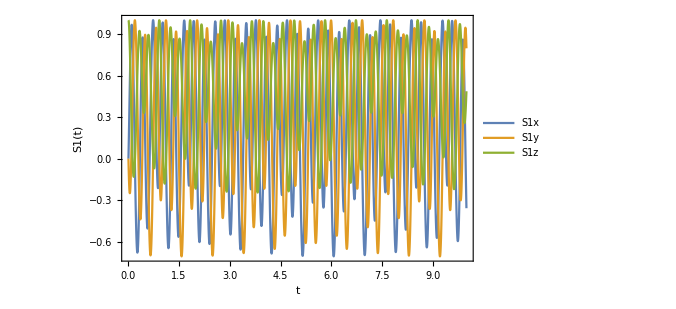

```mathematica
Plot[Evaluate[{S1x[t],S1y[t],S1z[t]}/. solution],{t,0,10},Frame->True,FrameLabel->{"t","S1(t)"},PlotLegends->Placed[{"S1x","S1y","S1z"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->All,WorkingPrecision->MachinePrecision,ImageSize->500]
```

```mathematica
S13D=ParametricPlot3D[Evaluate[{S1x[t],S1y[t],S1z[t]}/. solution],{t,0,10},PlotStyle->{Brown},TicksStyle->Medium,PlotRange->All,BoxRatios->{1,1,1},AxesLabel->{Style["x",Medium,Black],Style["y",Medium,Black],Style["z",Medium,Black]},ImageSize->500]
```

-Graphics3D-

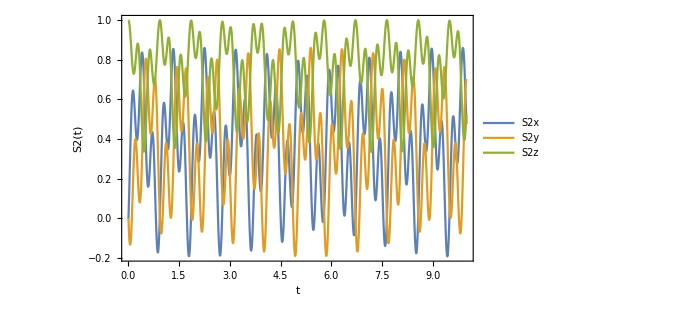

```mathematica
Plot[Evaluate[{S2x[t],S2y[t],S2z[t]}/. solution],{t,0,10},Frame->True,FrameLabel->{"t","S2(t)"},PlotLegends->Placed[{"S2x","S2y","S2z"},{Scaled[{0.1,1}],{-1,1}}],PlotRange->All,WorkingPrecision->MachinePrecision,ImageSize->500]
```

```mathematica
S23D=ParametricPlot3D[Evaluate[{S2x[t],S2y[t],S2z[t]}/. solution],{t,0,10},PlotStyle->{Black},TicksStyle->Medium,PlotRange->All,BoxRatios->{1,1,1},AxesLabel->{Style["x",Medium,Black],Style["y",Medium,Black],Style["z",Medium,Black]},ImageSize->500]
```

-Graphics3D-

```mathematica
Show[S13D,S23D]
```

-Graphics3D-